```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Desktop/Physics/Oxford/projects/correlator/2loop

```mathematica
<<LiteRed2`
(*<<Mint`*)
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Tue 1 Apr 2025 22:18:26
Read from:/Users/cesarecarlomella/Software/LiteRed2/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
convert=Table[ToExpression["topo"<>ToString[i]]-> ToExpression["IF"<>ToString[i]], {i,1,2}];
intfamvoc=Table[ToExpression["IF"<>ToString[i]],{i,1,2}];
```

## Integral family definition topo1

### Preliminaries

```mathematica
family = topo1;
```

```mathematica
SetDim[d];
Declare[
{p,k1,k2},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
intfam  = {sp[k1,k1]-m2, sp[k2,k2]-m2, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m2,sp[k1,k1]+sp[p,p] - 2 sp[k1,p]-m2,sp[k2,k2]+sp[p,p] +2 sp[k2,p]-m2}
props ={ "props"->{k1,k2,k1+k2, k1-p,k2+p  }, "every prop is massive with mass^2 "->{m2}, "invariant is p^2 = pp"}
Export["./definitions/props.m",props]
MI={j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]} /. j[topo1,a__] -> topo1[a];
Export["./definitions/masters.m", MI]
```

{-m2+k1·k1,-m2+k2·k2,-m2+k1·k1+2 k1·k2+k2·k2,-m2+pp+k1·k1-2 k1·p,-m2+pp+k2·k2+2 k2·p}

{props→{k1,k2,k1+k2,k1-p,k2+p},every prop is massive with mass^2 →{m2},invariant is p^2 = pp}

./definitions/props.m

./definitions/masters.m

```mathematica
(*(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1,k2},Directory->"topo1"]

GenerateIBP[family];

AnalyzeSectors[family];

FindSymmetries[family];

(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];

(*Save to disk*)
DiskSave[family];*)
```

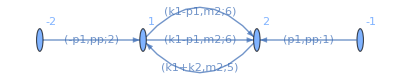

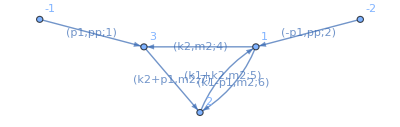

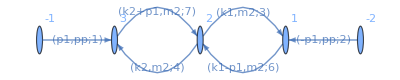

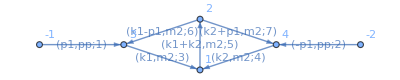

```mathematica
(*Import["./graphs/topo1/all/topo1_2_24.dot"]
Import["./graphs/topo1/all/topo1_3_28.dot"]
Import["./graphs/topo1/all/topo1_3_26.dot"]*)
Import["./graphs/topo1/all/topo1_3_14.dot"]
Import["./graphs/topo1/all/topo1_4_30.dot"]
Import["./graphs/topo1/all/topo1_4_27.dot"]
Import["./graphs/topo1/all/topo1_5_31.dot"]
```

```mathematica
Get["./topo1/topo1"];
```

```mathematica
MIs[family]
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
MIs[family]
mis=MIs[family];
tomis=ToMIsRule[mis];
(*Put[mis,"./Reduction/FamRed/"<>ToString[family]<>"/"<>"Mi"]
MIs[family];*)
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
(*LiteRed Masters*)
todiff= MIs[family];
```

```mathematica
(*diff eq for LiteRed Masters*)
derpp = Dinv[todiff,pp];
derm2 = Dinv[todiff,m2];
rhs=Union[Join[Union@Cases[derpp, j[family,a__],Infinity],Union@Cases[derm2, j[family,a__],Infinity]]];
rhsRed = Collect[IBPReduce[rhs],{_j}, Factor];
ReplaceRHS = Thread[Rule[rhs,rhsRed]];
redderpp=Collect[derpp/.ReplaceRHS, {_j},Factor];
redderm2=Collect[derm2/.ReplaceRHS, {_j},Factor];
MppLiteRed = CoefficientArrays[redderpp,todiff][[2]]//Normal;
Mm2LiteRed = CoefficientArrays[redderm2,todiff][[2]]//Normal;
```

```mathematica
MIs[family]
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
startBasis=Import["./rot/startBasis.m"] /. topo1[a__]-> j[topo1,a];
```

```mathematica
T=CoefficientArrays[(IBPReduce[startBasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ startBasis]//Together//Union;
invT = (Inverse[T]//Simplify);
Mpp=(D[T,pp].invT//Simplify) + T.MppLiteRed.(invT)//Simplify;
Mm2=(D[T,m2].invT//Simplify) + T.Mm2LiteRed.(invT)//Simplify;
Mpp=Mpp /. m2 -> 1 /. pp -> ρ /. d-> 4 -2 eps ;
Mm2=Mm2 /. m2 -> 1 /. pp -> ρ /. d-> 4 -2 eps ;
```

```mathematica
combineOperator = { F1[a__]F2[b__] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b] };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,eps,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
{sol[0][0], sol[0][1], coeff}=Import["./PERIODS/omega0.m"]/.extractPolySol;
d2omega0 = Import["./PERIODS/d2omega0.m"];
T1 = Import["./rot/T1.m"];
T1Inv= Inverse[T1]// Simplify;
T1derInv=D[ T1Inv /. ω0 -> ω0[ρ] /.dω0 -> D[ω0[ρ],ρ],ρ] /. ω0[ρ] ->ω0 /. ω0'[ρ]-> dω0/. ω0''[ρ]-> d2ω0 /.d2omega0  //Simplify;
EPS = Import["./rot/EPS.m"]
T2 = Import["./rot/T2.m"];
T2Inv= Inverse[T2]// Simplify;
T2derInv=D[ T2Inv  /. ω0 -> ω0[ρ],ρ]  /.d2omega0 /. ω0[ρ] ->ω0 /. ω0'[ρ]-> dω0 //Simplify;
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,eps,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
Mpp
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-(2 eps)/(√(4-ρ) √ρ),0,(2 eps)/(8-2 ρ),0,0,0,0,0},{0,0,0,0,1,0,0,0},{(6 eps^2)/((1-ρ) (9-ρ) ρ),0,0,-((-1-2 eps) (6-2 eps+(-2-2 eps) ρ))/(2 (1-ρ) (9-ρ) ρ),(-9 (2-2 eps)-10 (-4-2 eps) ρ+3 (-2-2 eps) ρ^2)/(2 (1-ρ) (9-ρ) ρ),0,0,0},{0,-eps/(√((4-ρ) ρ)),0,(-4-2 eps)/(6 √((4-ρ) ρ)),-(5 ρ)/(3 √((4-ρ) ρ)),(2 eps)/(8-2 ρ),0,0},{0,0,(4 eps)/(√(4-ρ) √ρ),0,0,0,(2 eps)/(4-ρ),0},{0,0,0,-(2 eps (6-ρ))/(72-24 ρ),0,-(3 eps)/(4 (3-ρ) √((4-ρ) ρ)),-(2 eps)/(96-32 ρ),-eps/(-3+ρ)}}

```mathematica
newMpp[1]=(T1derInv.T1 //Simplify)+T1Inv.Mpp.T1   /. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
newMpp[2]=Inverse[EPS].newMpp[1].EPS   /. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
newMpp[3]=(T2derInv.T2//Simplify)+T2Inv.newMpp[2].T2   /. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
```

```mathematica
newMpp[3]/. eps -> 0//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(10 dω0 ρ (9-10 ρ+ρ^2)+4 (9-10 ρ+ρ^2) ω0)/(6 (-9+ρ) (-1+ρ) √(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*EllipticPi[ ... ] *)
```

```mathematica
(*4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2)))*)
```

```mathematica
g4derdef
```

g4'[ρ]→(2 ρ (1+ρ) ω0)/(3 ((4-ρ) ρ)^(3/2))

```mathematica
Integral[1/Sqrt[Y],]
```

```mathematica
g4derdef = Import["./rot/g4def.m"];
```

```mathematica
R = Import["./rot/R.m"];
Rinv = Inverse[R]// Simplify
derRinv=(D[Rinv, ρ] // Simplify)/. ω0[ρ] ->ω0 /. ω0'[ρ]-> dω0/. ω0''[ρ]-> d2ω0 /.d2omega0  /. g4derdef// Simplify;
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,-g4[ρ]+(5 ρ ω0[ρ])/(3 √(-((-4+ρ) ρ))),0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
newMpp[4]=(derRinv.R//Simplify)+Rinv.newMpp[3].R  /.ω0[ρ]-> ω0/. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
```

```mathematica
newMpp[4] //Simplify //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (eps (-8 √(-((-4+ρ) ρ)) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | 0 | 0 | -(eps (ρ (9-10 ρ+ρ^2) ω0+9 √(-((-4+ρ) ρ)) g4[ρ]))/(12 (-4+ρ) (-3+ρ) ρ) | 0 | (3 eps)/(4 (-3+ρ) √(-((-4+ρ) ρ))) | eps/(16 (-3+ρ)) | -eps/(-3+ρ))

```mathematica
Export["./rot/epsilon_factorised.m",newMpp[4]]
```

./rot/epsilon_factorised.m

```mathematica
adjustconventions={ √(-((-4+ρ) ρ)) -> Sqrt[(4-ρ)]Sqrt[ρ], 1/√(-((-4+ρ) ρ)) -> 1/ Sqrt[(4-ρ)]/Sqrt[ρ], 1/(ρ-4) -> -1/(4-ρ)}
LogForms = {(9+10 ρ-3 ρ^2)/(2 (-9+ρ) (-1+ρ) ρ),1/(-3+ρ) /√(4-ρ)/Sqrt[ρ],1/(4-ρ),1/√(4-ρ)/Sqrt[ρ],1/(-3+ρ)}/.adjustconventions;
Ellforms =  { g4[ρ]/((-9+ρ) (-1+ρ) ρ ω0^2) ,((3+ρ)^4 ω0^2)/((-9+ρ) (-1+ρ) ρ) ,(-8 √(4-ρ)Sqrt[ρ] (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ])/((-9+ρ) (-4+ρ)^2 (-1+ρ) ρ)   , 1/((-9+ρ) (-1+ρ) ρ ω0^2),(ρ (9-10 ρ+ρ^2) ω0+9 √(4-ρ)Sqrt[ρ] g4[ρ])/((4-ρ) (-3+ρ) ρ), ω0 }/.adjustconventions;
nameLogForm = Thread[Rule[LogForms, Table[l[i],{i,1,Length[LogForms]}]]]
nameEllForm = Thread[Rule[Ellforms, Table[EF[i],{i,1,Length[Ellforms]}]]]
```

{√(-((-4+ρ) ρ))→√(4-ρ) √ρ,1/(√(-((-4+ρ) ρ)))→1/(√(4-ρ) √ρ),1/(-4+ρ)→-1/(4-ρ)}

{(9+10 ρ-3 ρ^2)/(2 (-9+ρ) (-1+ρ) ρ)→l[1],1/(√(4-ρ) (-3+ρ) √ρ)→l[2],1/(4-ρ)→l[3],1/(√(4-ρ) √ρ)→l[4],1/(-3+ρ)→l[5]}

{g4[ρ]/((-9+ρ) (-1+ρ) ρ ω0^2)→EF[1],((3+ρ)^4 ω0^2)/((-9+ρ) (-1+ρ) ρ)→EF[2],(-8 √(4-ρ) √ρ (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ])/((-9+ρ) (-4+ρ)^2 (-1+ρ) ρ)→EF[3],1/((-9+ρ) (-1+ρ) ρ ω0^2)→EF[4],(ρ (9-10 ρ+ρ^2) ω0+9 √(4-ρ) √ρ g4[ρ])/((4-ρ) (-3+ρ) ρ)→EF[5],ω0→EF[6]}

```mathematica
Export["./FORMS/log_forms.m", nameLogForm]
Export["./FORMS/ell_forms.m", nameEllForm]
```

./FORMS/log_forms.m

./FORMS/ell_forms.m

```mathematica
ser=Series[nameLogForm[[;;,1]], {ρ,0,40}]//Normal;
```

```mathematica
omega0Sol=ω0-> sol[0][0 ] /. extractPolySol;
g4Series=g4[ρ]-> Collect[Integrate[Series[g4derdef[[2]] /. omega0Sol, {ρ,0,39}]//Normal, ρ], {ρ}, Simplify] /. ρ^a_ /; a> 39 -> 0;
EllSeries=Series[nameEllForm[[;;,1]] /. omega0Sol /. g4Series, {ρ,0,39}]//Normal;
```

```mathematica
ExpansionMat=Collect[Series[newMpp[4] /. eps -> 1  /. g4Series/.nameEllForm /. nameLogForm /.Thread[Rule[nameLogForm[[;;,2]],ser]] /. Thread[Rule[nameEllForm[[;;,2]],EllSeries]], {ρ,0,39}]//Normal, {ρ},Simplify];
```

```mathematica
Series[ExpansionMat, {ρ,0,0}]//Normal
(Coefficient[%,ρ,-1].{i1,i2,i3,i4,i5,i6,i7,i8}//Union)[[2;;]]
(*i5 -> -1/2i4 *)
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-1/(√ρ),0,1/4,0,0,0,0,0},{0,0,0,10/9+1/(2 ρ),4/9+1/ρ,0,0,0},{2/3,0,0,7/9+1/(4 ρ),10/9+1/(2 ρ),0,0,0},{0,-1/(2 √ρ),0,-1/(4 √ρ),-1/(6 √ρ),1/4,0,0},{0,0,2/(√ρ),0,0,0,1/2,0},{0,0,0,-1/12,0,-1/(8 √ρ),-1/48,1/3}}

{i4/4+i5/2,i4/2+i5}

## Solutions

#### Boundary Condition

Explicit integrals

```mathematica
props
```

{props→{k1,k2,k1+k2,k1-p,k2+p},every prop is massive with mass^2 →{m2},invariant is p^2 = pp}

```mathematica
Tad[n_]:=E^(EulerGamma eps)(-1 )(m2)^((d-2n)/2)Gamma[n-d/2]/Gamma[n] 
(*Series[eps Tad[2] /. d ->4-2eps, {eps,0,3}]// FullSimplify*)
cantedExp =(Collect[Series[Tad[2] /.m2 -> 1/. d -> 4 -2 eps//Simplify, {eps,0,5}]//Normal, {eps}, FullSimplify]);
```

```mathematica
FeynmanParam2[props_List, loops_List, powprop_List,
							 kinematics_List] /; (Length[powprop] == Length[props]) :=
					    Block[{Nl = Length[loops], Npp = Total[powprop], xs = Table[x[i], {i, Length[props]}], 
					       den, A, B, C, matA, vecB, Fpoly,
						   Upoly, Aminor, integrand, d, Prefact},
					      den = xs.props;
					      den = (den // ExpandAll) //. kinematics//Expand;                                                                                                     
						     A[i_, i_] := Coefficient[den, loops[[i]]^2];
						     A[i_, j_] /; i =!= j := 1/2 Coefficient[den, loops[[i]] loops[[j]]];
						     matA = Table[A[i, j], {i, Nl}, {j, Nl}] // Expand;                                                                                   
						     B[i_] := Coefficient[den, loops[[i]]]/2 /. (Rule[#, 0] & /@ loops);
						     vecB = Table[B[i], {i, Nl}] // Expand;                                                                                               
						     Aminor = Det[matA]*Inverse[matA] // Simplify;                                                                                        
						     C = den /. (Rule[#, 0] & /@ loops);
						     Upoly = Det[matA];
						     Fpoly = ((vecB.Aminor.vecB) - Upoly C // ExpandAll) /. kinematics;   
							      Prefact = (-1)^(Npp) Gamma[Npp- Nl d/ 2] / Product[Gamma[i],{i,powprop}]; 			  
  integrand =     Prefact* Product[x[i]^(powprop[[i]] - 1), {i, 1, Length[props]}] Upoly^(Npp - (Nl + 1)*d/2)/Fpoly^(Npp - Nl*d/2); {{"U", "F", "Int"}, {Upoly, Fpoly, integrand}} ]
```

```mathematica
propFeynman = {k[1]^2-m2, (k[1]-p[1])^2-m2};
par=FeynmanParam2[propFeynman, {k[1]}, {1,2}, {p[1]^2->pp}];
```

```mathematica
(*Integrate[par[[2,3]]/. pp -> 0 /. m2-> 1 /. x[1]-> 1-x[2], {x[2],0,1}]// FullSimplify*)
```

```mathematica
bub[0]=Series[E^(eps EulerGamma)par[[2,3]] /. pp -> 0  /. x[2]-> 1-x[1]/. d-> 4-2eps/. m2-> 1, {eps,0,5}]//FullSimplify//Normal;
```

-x[1]-1/12 eps^2 π^2 x[1]-1/160 eps^4 π^4 x[1]+1/3 eps^3 x[1] Zeta[3]+1/180 eps^5 x[1] (5 π^2 Zeta[3]+36 Zeta[5])

```mathematica
(*family = bub;
SetDim[d];
Declare[
{p,k1},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
intfam  = {sp[k1,k1]-m2,sp[k1,k1] + sp[p,p] + 2 sp[p,k1] -m2}
(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1},Directory->"bub"]
GenerateIBP[family];
AnalyzeSectors[family];
FindSymmetries[family];
(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];
(*Save to disk*)
DiskSave[family];
laporta ={ j[bub,0,1], j[bub,1,1]};
canonB ={ eps j[bub,0,2],eps √(4-pp) √pp j[bub,2,1]};
der=(Dinv[canonB,pp]//IBPReduce) /. m2 -> 1 /. pp -> ρ;dermat=(CoefficientArrays[der, laporta][[2]]//Normal);
T=CoefficientArrays[IBPReduce[canonB]/.m2-> 1 /. pp -> ρ,laporta ][[2]]//Normal;
deq =(dermat.Inverse[T]/. d-> 4 -2 eps //Simplify)/. 1/√(-((-4+ρ) ρ)) -> 1/√(4-ρ)/Sqrt[ρ]/.eps :> 1;
deq  //MatrixForm*)
```

```mathematica
deq ={{0,0},{-1/(√(4-ρ) √ρ),1/(4-ρ)}};
(*
laporta =  Laporta2CanonBub . CanonB
*)
Laporta2CanonBub={{2/((-2+d) eps),0},{1/((-3+d) eps),(√(4-ρ))/((-3+d) eps √ρ)}}/.d-> 4-2eps//Simplify//Factor;
Canon2LaportaBub=Inverse[Laporta2CanonBub]//Simplify;
laporta={j[bub,0,1],j[bub,1,1]};
canonB={eps j[bub,0,2],eps √(4-ρ) √ρ j[bub,2,1]};
```

```mathematica
Laporta2CanonBub
```

{{-1/((-1+eps) eps),0},{-1/(eps (-1+2 eps)),-(√(4-ρ))/(eps (-1+2 eps) √ρ)}}

```mathematica
bub[0]=Series[E^(eps EulerGamma)par[[2,3]] /. pp -> 0  /. x[2]-> 1-x[1]/. d-> 4-2eps/. m2-> 1, {eps,0,5}]//FullSimplify//Normal;
```

```mathematica
deqNamed=deq/. nameLogForm
```

{{0,0},{-l[4],l[3]}}

```mathematica
(*The canonical bubble vanish in the limit of 0 momentum *)
const = {Collect[Series[eps Tad[2] /. m2-> 1/. d-> 4 -2 eps, {eps,0,6}]//Normal, {eps}, FullSimplify],0}
```

{-1-(eps^2 π^2)/12-(eps^4 π^4)/160+1/3 eps^3 Zeta[3]+eps^6 (-(61 π^6)/120960-Zeta[3]^2/18)+eps^5 (1/36 π^2 Zeta[3]+Zeta[5]/5),0}

```mathematica
sol0 =Coefficient[const,eps,0]II[];
sol1 = (deqNamed.sol0 /. II[]l[a_] -> II[l[a]]) + Coefficient[const,eps,1];
sol2 = (Expand[deqNamed.sol1 ]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]}) + Coefficient[const,eps,2];
sol3 = (Expand[deqNamed.sol2] /. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]}) + Coefficient[const,eps,3];
sol4 = (Expand[deqNamed.sol3] /. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]}) + Coefficient[const,eps,4];
sol5 = (Expand[deqNamed.sol4 ]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]}) + Coefficient[const,eps,5];
```

```mathematica
FULLSOLbubTad = sol0 + eps sol1 + eps^2 sol2 + eps^3 sol3 +eps^4 sol4+eps^5 sol5;
```

```mathematica
(*Export["./solutions/bubtad/canon_basis.m", canonB];
Export["./solutions/bubtad/laporta.m", laporta];
Export["./solutions/bubtad/Laporta2CanonBub.m",Laporta2CanonBub];
Export["./solutions/bubtad/sol.m", FULLSOLbubTad];*)
```

Two loop tadpole-sunrise

```mathematica
startBasis[[2]]
```

3 (-4+d)^2 m2 j[topo1,0,0,1,2,2]

```mathematica
propFeynman = {k[1]^2-m2, k[2]^2-m2, (k[1]-k[2])^2-m2 };
par=FeynmanParam2[propFeynman, {k[1],k[2]}, {1,1,1}, {}];
```

```mathematica
toint=par[[2,3]] /. m2-> 1//Simplify
```

-(Gamma[3-d] (x[2] x[3]+x[1] (x[2]+x[3]))^(-3 d/2) (x[1]^2 (x[2]+x[3])+x[2] x[3] (x[2]+x[3])+x[1] (x[2]^2+3 x[2] x[3]+x[3]^2))^d)/(x[1]+x[2]+x[3])^3

```mathematica
Collect[x[1]-x[1]^2+x[3]-x[1] x[3]-x[3]^2, {x[1]}]
```

-x[1]^2+x[1] (1-x[3])+x[3]-x[3]^2

```mathematica
toint /. {x[2] -> 1-x[3]-x[1]} // Simplify
Integrate[%, {x[1],0,1}, Assumptions->{0<x[3]<1 && d< 0}]
```

-Gamma[3-d] (x[1]-x[1]^2+x[3]-x[1] x[3]-x[3]^2)^(-d/2)

1/(1+√((1-x[3])/(1+3 x[3])))(Beta[1/2 (1+√((1-x[3])/(1+3 x[3]))),1-d/2,1-d/2]-Beta[(-1-x[3]+√(1+(2-3 x[3]) x[3]))/(2 √(1+(2-3 x[3]) x[3])),1-d/2,1-d/2]) Gamma[3-d] (1+(2-3 x[3]) x[3])^(-d/2) (-1+x[3]-√(1+(2-3 x[3]) x[3]))

```mathematica
toint=par[[2,3]] /. x[3]-> 1//FullSimplify
Integrate[toint, {x[1],0,1}]
toint =par[[2,3]] /. x[3]-> 1-x[1]//FullSimplify
```

(Gamma[6-d] x[1] x[2] (x[2]+x[1] (1+x[2]))^(-3 d/2) (m2 (1+x[1]+x[2]) (x[2]+x[1] (1+x[2])))^d)/(m2^6 (1+x[1]+x[2])^6)

$Aborted

-(Gamma[6-d] (-1+x[1]) x[1] x[2] (-m2 ((-1+x[1]) x[1]-x[2]) (1+x[2]))^d (x[1]-x[1]^2+x[2])^(-3 d/2))/(m2^6 (1+x[2])^6)

Boundary conditions

```mathematica
amflow = Import["./amflow/amflow_solution.m"];
amflow=Thread[Rule[amflow[[;;,1]],Series[amflow[[;;,2]]Normal[Series[E^(2 EulerGamma eps), {eps,0,8}]], {eps,0,5}]//Normal]];
```

```mathematica
N[amflow[[1,2]],20]
Series[(Collect[Series[ Tad[1] /.m2 -> 1/. d -> 4 -2 eps//Simplify, {eps,0,8}]//Normal, {eps}, FullSimplify])^2, {eps,0,5}]//Normal//N
%%-%//Chop
```

4.6449340668482264365+1./eps^2+2./eps+6.488496864923390016 eps+10.226125321993045431 eps^2+12.230779776807155463 eps^3+16.527634369423609977 eps^4+18.336268252496154743 eps^5

4.64493+1/eps^2+2./eps+6.4885 eps+10.2261 eps^2+12.2308 eps^3+16.5276 eps^4+18.3363 eps^5

0

```mathematica
basisCanon=Inverse[R].Inverse[T2].Inverse[EPS].Inverse[T1].startBasis/.d-> 4-2eps//Simplify;
```

```mathematica
(* boundary constants *)
(*
The first integral has a non trivial expansion 
2nd integral starts at O(eps^2) 
3nd integral is = 0 to all orders
4nd integral starts at O(eps^2)
5nd integral starts at O(eps^2)
6nd integral is  0 to all orders
7nd integral is  0 to all orders
8nd integral is  0 to all orders
*)
Series[(basisCanon[[1]]//IBPReduce)/. m2-> 1 /. j[topo1,0,0,0,1,1]-> Tad[1]^2 /. m2-> 1 /. d-> 4 -2 eps, {eps,0,6}]//Normal//FullSimplify
Series[(basisCanon[[2]]//IBPReduce) /. d -> 4 -2 eps /. m2 -> 1 /. amflow, {eps,0,4}]//Normal
Series[(basisCanon[[3]]//IBPReduce) /. d -> 4 -2 eps /. m2 -> 1 /. amflow /. pp -> 0, {eps,0,4}]//Normal
Series[(basisCanon[[4]] // IBPReduce)/. d -> 4 -2 eps /. m2 -> 1/. pp -> 0 /. amflow /. omega0Sol /. ρ -> 0, {eps,0,4}]
Series[(basisCanon[[5]] // IBPReduce)/. d -> 4 -2 eps /. m2 -> 1/. pp -> 0 /. amflow /. omega0Sol /. ρ -> 0, {eps,0,4}]
Series[Series[(Series[(basisCanon[[6]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
Series[Series[(Series[(basisCanon[[7]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
Series[Series[(Series[(basisCanon[[8]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
```

4+(2 eps^2 π^2)/3+(7 eps^4 π^4)/90+(31 eps^6 π^6)/3780-4/9 eps^3 (6+eps^2 π^2) Zeta[3]+8/9 eps^6 Zeta[3]^2-8/5 eps^5 Zeta[5]

-9.375628954757835562406249155489108276381612038543425042665200755602643815819418617114434849986518332252508203078108429 eps^2+16.15030452706328802053930248293475300269471564328464438444235958883895845622280017956586493972990829418056296744823522 eps^3-47.592539527227664743904938898757931873066839650663242985388381413061148668650009497141538640969083510090096651611060902 eps^4

0

-9.375628954757835562406249155489108276381612038543425042665200755602643815819418617114434849986518332252508203078108429 eps^2+16.15030452706328802053930248293475300269471564328464438444235958883895845622280017956586493972990829418056296744823522 eps^3-47.5925395272276647439049388987579318730668396506632429853883814130611486686500094971415386409690835100900966516110609 eps^4+O[eps]^5

4.687814477378917781203124577744554138190806019271712521332600377801321907909709308557217424993259166126254101539054215 eps^2-8.075152263531644010269651241467376501347357821642322192221179794419479228111400089782932469864954147090281483724117612 eps^3+23.79626976361383237195246944937896593653341982533162149269419070653057433432500474857076932048454175504504832580553045 eps^4+O[eps]^5

√O[ρ]

0

0

```mathematica
const = {4+(2 eps^2 π^2)/3+(7 eps^4 π^4)/90+(31 eps^6 π^6)/3780-4/9 eps^3 (6+eps^2 π^2) Zeta[3]+8/9 eps^6 Zeta[3]^2-8/5 eps^5 Zeta[5], 0,0,0,0,0,0,0}
```

{4+(2 eps^2 π^2)/3+(7 eps^4 π^4)/90+(31 eps^6 π^6)/3780-4/9 eps^3 (6+eps^2 π^2) Zeta[3]+8/9 eps^6 Zeta[3]^2-8/5 eps^5 Zeta[5],0,0,0,0,0,0,0}

#### formal solution

```mathematica
Deq = Import["./rot/epsilon_factorised.m"] /.adjustconventions;
DeqNamed = Deq /.nameEllForm  /. nameLogForm /. eps ->1;
```

```mathematica
c[0] =Coefficient[const,eps,0] II[];
c[1] = Coefficient[const,eps,1]II[];
c[2] = Coefficient[const,eps,2]II[];
c[3] = Coefficient[const,eps,3]II[];
c[4] = Coefficient[const,eps,4]II[];
tmp1 = DeqNamed.c[0]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]} ;
sol1  = tmp1 + c[1];
tmp1 = DeqNamed.sol1/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol2  = tmp1 + c[2];
tmp1 = DeqNamed.sol2/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol3  = tmp1 + c[3];
tmp1 = DeqNamed.sol3/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol4  = tmp1 + c[4];
```

```mathematica
FU
```

FU

```mathematica
FULLSOL=c[0] + eps sol1 + eps^2 sol2 + eps^3 sol3 + eps^4 sol4 /. II[] -> 1;
```

## Corr

```mathematica
CanBasisRed[[1]]
FULLSOL[[1]]
```

4 (-1+eps)^2 eps^4 j[topo1,0,0,0,1,1]

4+(2 eps^2 π^2)/3+(7 eps^4 π^4)/90-8/3 eps^3 Zeta[3]

```mathematica
CanBasisRed= Collect[IBPReduce[basisCanon]/.pp -> ρ /. m2 -> 1/.d-> 4-2eps, {_j },Simplify];
Union@Cases[CanBasisRed, _j, ∞];
laporta = MIs[topo1];
Complement[%%,%]
mat=CoefficientArrays[CanBasisRed,laporta][[2]]//Normal;
invmat=Inverse[mat]//Simplify;
```

```mathematica
int=Integrate[(1 - x(1-x) ρ )^-ϵ, {x,0,1}, Assumptions->{ρ<0}]/.√(-ρ/(-4+ρ))-> √(ρ/(4-ρ))
```

1/((-1+ϵ) √-ρ)2^(-1-ϵ) ((√(4-ρ)-√-ρ) (1+√(ρ/(-4+ρ)))^ϵ Hypergeometric2F1[1-ϵ,ϵ,2-ϵ,1/2 (1-√(ρ/(-4+ρ)))]-(√(4-ρ)+√-ρ) (1-√(ρ/(-4+ρ)))^ϵ Hypergeometric2F1[1-ϵ,ϵ,2-ϵ,1/2 (1+√(ρ/(-4+ρ)))])

```mathematica
int=Integrate[(1 - x(1-x) ρ )^-ϵ, {x,0,1}, Assumptions->{4>ρ>0}]/.√(-ρ/(-4+ρ))-> √(ρ/(4-ρ))
```

(ⅈ (4-ρ)^(1/2-ϵ) (Beta[1/2 (1-ⅈ √(ρ/(4-ρ))),1-ϵ,1-ϵ]-Beta[1/2 (1+ⅈ √(ρ/(4-ρ))),1-ϵ,1-ϵ]))/(√ρ)

```mathematica
(1+(ⅈ √ρ)/(√(4-ρ)))(1-(ⅈ √ρ)/(√(4-ρ)))//FullSimplify
```

-4/(-4+ρ)

```mathematica
TrigToExp[ArcTan[(√ρ)/(√(4-ρ))]]
```

1/2 ⅈ Log[1-(ⅈ √ρ)/(√(4-ρ))]-1/2 ⅈ Log[1+(ⅈ √ρ)/(√(4-ρ))]

```mathematica
(Series[int, {ϵ,0,1}] /.√(-ρ/(-4+ρ)) -> Sqrt[ρ]/Sqrt[4-ρ] /.√(ρ/(4-ρ))-> Sqrt[ρ]/√(4-ρ)//FullSimplify) (*/.Log[1-(ⅈ √ρ)/(√(4-ρ))]-> Log[4/(4-ρ)] - Log[(1+(ⅈ √ρ)/(√(4-ρ)))] *)
```

1+(1-Log[2]+1/(2 √-ρ)(-((√(4-ρ)-√-ρ) (Log[1+√(ρ/(-4+ρ))]-Hypergeometric2F1^(0,0,1,0)[1,0,2,1/2 (1-√(ρ/(-4+ρ)))]+Hypergeometric2F1^(0,1,0,0)[1,0,2,1/2 (1-√(ρ/(-4+ρ)))]-Hypergeometric2F1^(1,0,0,0)[1,0,2,1/2 (1-√(ρ/(-4+ρ)))]))+(√(4-ρ)+√-ρ) (Log[1-√(ρ/(-4+ρ))]-Hypergeometric2F1^(0,0,1,0)[1,0,2,1/2 (1+√(ρ/(-4+ρ)))]+Hypergeometric2F1^(0,1,0,0)[1,0,2,1/2 (1+√(ρ/(-4+ρ)))]-Hypergeometric2F1^(1,0,0,0)[1,0,2,1/2 (1+√(ρ/(-4+ρ)))]))) ϵ+O[ϵ]^2

```mathematica
coupl = λ^2
```

λ^2

```mathematica
Amp = Collect[1/2j[topo1,1,1,1,1,1] + 1/2 j[topo1,2,1,1,1,0] // IBPReduce, {_j}, Together];
(* Amp = AmpRedCanon . CANON *)
AmpRedCanon=(CoefficientArrays[Amp /. m2 -> 1 /. pp -> ρ, laporta][[2]]//Normal).invmat /. d -> 4 -2 eps//Simplify
```

{0,(3+eps (-6+ρ)-2 ρ)/(32 (1-2 eps)^2 eps^2 ρ),(1+eps (-6+ρ))/(16 (1-2 eps)^2 eps^2 √(-((-4+ρ) ρ))),-((-4+ρ) (2 dω0 ρ (9-10 ρ+ρ^2)+(9-6 ρ+2 ρ^2+eps (-9-3 ρ+ρ^2)) ω0)-3 √(-((-4+ρ) ρ)) (5-2 ρ+eps (2+ρ)) g4[ρ]+5 ρ (5-2 ρ+eps (2+ρ)) ω0[ρ])/(96 (1-2 eps)^2 eps^2 (-4+ρ) ρ),-3/(16 (1-2 eps)^2 eps ρ ω0),-(5-2 ρ+eps (2+ρ))/(32 (1-2 eps)^2 eps^2 √(-((-4+ρ) ρ))),0,-1/(2 eps^3 ρ-4 eps^4 ρ)}

```mathematica
AmpRedCanon.Table[canon[i],{i,1,8}]
```

((3+eps (-6+ρ)-2 ρ) canon[2])/(32 (1-2 eps)^2 eps^2 ρ)+((1+eps (-6+ρ)) canon[3])/(16 (1-2 eps)^2 eps^2 √(-((-4+ρ) ρ)))-(3 canon[5])/(16 (1-2 eps)^2 eps ρ ω0)-((5-2 ρ+eps (2+ρ)) canon[6])/(32 (1-2 eps)^2 eps^2 √(-((-4+ρ) ρ)))-canon[8]/(2 eps^3 ρ-4 eps^4 ρ)-1/(96 (1-2 eps)^2 eps^2 (-4+ρ) ρ)canon[4] ((-4+ρ) (2 dω0 ρ (9-10 ρ+ρ^2)+(9-6 ρ+2 ρ^2+eps (-9-3 ρ+ρ^2)) ω0)-3 √(-((-4+ρ) ρ)) (5-2 ρ+eps (2+ρ)) g4[ρ]+5 ρ (5-2 ρ+eps (2+ρ)) ω0[ρ])

```mathematica
bareCorrelator=Collect[Series[(Series[AmpRedCanon, {eps,0,4}]//Normal).FULLSOL, {eps,0,-1}]//Normal, {eps, _II}, Simplify]/.adjustconventions;
```

```mathematica
Union@Cases[Collect[(AmpRedCanon).FULLSOL//Normal, {eps, _II}, Simplify], _II, ∞]
```

{II[EF[6]],II[l[4]],II[EF[1],EF[6]],II[EF[4],EF[6]],II[l[1],EF[6]],II[l[3],l[4]],II[EF[1],l[1],EF[6]],II[EF[2],EF[4],EF[6]],II[EF[3],EF[4],EF[6]],II[EF[4],l[1],EF[6]],II[EF[5],EF[4],EF[6]],II[l[1],EF[4],EF[6]],II[l[1],l[1],EF[6]],II[l[2],EF[1],EF[6]],II[l[3],EF[1],EF[6]],II[l[3],l[3],l[4]],II[l[3],l[4],l[4]],II[l[4],l[3],l[4]],II[l[5],l[4],l[4]]}

```mathematica
Coefficient[bareCorrelator, eps,-2]
Coefficient[bareCorrelator, eps,-1]
(*Coefficient[bareCorrelator, eps,0]
Coefficient[bareCorrelator, eps,1]*)
```

0

-II[l[4]]/(2 √(4-ρ) √ρ)

## Baikov Stuff

```mathematica
Import["~/Software/DlogBasis/DlogBasis.wl"]
```

DlogBasis: Package for automated calculation of leading singularities and dlog integrands.
Pascal Wasser, Johannes Gutenberg University Mainz (2020).

```mathematica
Import["~/Software/Baikov/Baikov.m"]
```

H. Frellesvig and C.G.Papadopoulos: arXiv:1701.07356 [hep-ph]

This is a Mathematica Script for the Baikov representation

The main routine is Baikov[L_,E1_,propagators_,external_]

The input is:

L: the number of loops

E1: the number of independent external momenta

propagators: a list in the form {(k[1])^2-m1,...,(k[2]+p[1])^2-m2, ...} containing L(L+1)/2+L*E independent propagators

external: a list in the form {s[2,2]-> S1, ...} with replacement rules for the external invariants

starting at s[n,n] with n=L+1

Example 1-loop 3-point:

Propagators={k[1]^2-m1,(k[1]+p[1])^2-m2,(k[1]+p[1]+p[2])^2-m3}

repl={s[2,2]→S1,s[3,3]→S2,s[2,3]→(S3-S1-S2)/2}

Baikov[1,2,Propagators,repl]

```mathematica
Propagators={k[1]^2 -m2, k[2]^2-m2, (k[1]+k[2])^2 -m2 ,(k[1]-p[1])^2-m2,(k[2]+p[1])^2-m2 }
```

{-m2+k[1]^2,-m2+k[2]^2,-m2+(k[1]+k[2])^2,-m2+(k[1]-p[1])^2,-m2+(k[2]+p[1])^2}

```mathematica
MIs[mybasis]
```

MIs[mybasis]

```mathematica
baik=Baikov[2,1, Propagators, {s[3,3]-> pp2}];
```

M1=3    N1=5

{1,2,3,4,5}

rules   {k[1]^2→s[1,1],k[1] k[2]→s[1,2],k[1] k[2]→s[2,1],k[2]^2→s[2,2],k[1] p[1]→s[1,3],k[2] p[1]→s[2,3],k[1] p[1]→s[3,1],k[2] p[1]→s[3,2],p[1]^2→s[3,3]}

{s[3,3]→pp2}

rulesf {f[1]→-m2,f[2]→-m2,f[3]→-m2,f[4]→-m2+s[3,3],f[5]→-m2+s[3,3]}

test1 {0,0,0,0,0}

nums  {{{1,1,1},{1,2,2},{1,3,3}},{{2,2,4},{2,3,5}}}

{s[1,1]→m2+dd$20268[1],s[1,2]→1/2 (-m2-dd$20268[1]-dd$20268[2]+dd$20268[3]),s[1,3]→1/2 (dd$20268[1]-dd$20268[4]+s[3,3]),s[2,2]→m2+dd$20268[2],s[2,3]→1/2 (-dd$20268[2]+dd$20268[5]-s[3,3])}

Id  {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}Det-8

test2  {s[1,1],s[1,2],s[1,3],s[2,2],s[2,3]}

Gramm  pp2

test3  1 3

10

test3  0

test3  1 2

10

test3  0

test3  1 1

8

test3  0

test3  2 3

10

test3  0

test3  2 2

8

test3  0

test3  2 1

10

test3  0

test4  {{{1,1,0},{1,2,0},{1,3,0}},{{2,1,0},{2,2,0},{2,3,0}}}

test5  {{{1,1,0},{1,2,0},{1,3,0}},{{2,1,0},{2,2,0},{2,3,0}},{{3,1,0},{3,2,0},{3,3,0}}}

```mathematica
baikov=baik[[3]]//PowerExpand // FullSimplify//PowerExpand//FullSimplify
```

2^(4-d) pp2^(1-d/2) (3 m2^2 pp2-pp2^2 x[3]-x[2] (x[1] (x[3]-x[4])+x[4] (x[2]-x[3]+x[4]))+(x[1] (-x[1]+x[2]+x[3])+(x[1]+x[2]-x[3]) x[4]) x[5]-x[1] x[5]^2+pp2 (x[2] (x[3]+x[4]-x[5])+x[1] (x[3]-x[4]+x[5])+x[3] (-x[3]+x[4]+x[5]))+m2 (-pp2^2-x[1]^2-x[2]^2-x[2] x[4]-x[4]^2+x[1] (x[2]+2 x[4]-x[5])+(2 x[2]+x[4]) x[5]-x[5]^2+pp2 (x[1]+x[2]+2 x[3]+x[4]+x[5])))^(1/2 (-4+d))

```mathematica
Union@Cases[-SP[k[1],p[1]] SP[k[2],k[2]] SP[p[1],k[1]]+SP[k[1],k[2]] SP[k[2],p[1]] SP[p[1],k[1]]+SP[k[1],p[1]] SP[k[2],k[1]] SP[p[1],k[2]]-SP[k[1],k[1]] SP[k[2],p[1]] SP[p[1],k[2]]-SP[k[1],k[2]] SP[k[2],k[1]] SP[p[1],p[1]]+SP[k[1],k[1]] SP[k[2],k[2]] SP[p[1],p[1]], _SP,∞]
```

{SP[k[1],k[1]],SP[k[1],k[2]],SP[k[1],p[1]],SP[k[2],k[1]],SP[k[2],k[2]],SP[k[2],p[1]],SP[p[1],k[1]],SP[p[1],k[2]],SP[p[1],p[1]]}

```mathematica
Solve[Thread[Equal[(Propagators//Expand) /. k[1]^2  -> SP[k[1],k[1]] /. k[2]^2 -> SP[k[2],k[2]] /. k[1]k[2] -> SP[k[1],k[2]] /. k[1]p[1]-> SP[p[1],k[1]]  /. p[1]^2 -> pp /. k[2]p[1]-> SP[p[1],k[2]],{x[1],x[2],x[3],x[4],x[5]}]], {SP[k[1],k[1]],SP[k[1],k[2]],SP[k[1],p[1]],SP[k[2],k[1]],SP[k[2],k[2]],SP[k[2],p[1]],SP[p[1],k[1]],SP[p[1],k[2]]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{SP[k[1],k[1]]→m2+x[1],SP[k[1],k[2]]→1/2 (-m2-x[1]-x[2]+x[3]),SP[k[2],k[2]]→m2+x[2],SP[p[1],k[1]]→1/2 (pp+x[1]-x[4]),SP[p[1],k[2]]→1/2 (-pp-x[2]+x[5])}}

```mathematica
moms = {k[1],k[2],p[1]}
Det[Table[SP[mom1,mom2], {mom1,moms}, {mom2,moms}]] /. SP[p[1],p[1]]-> pp
```

{k[1],k[2],p[1]}

-pp SP[k[1],k[2]] SP[k[2],k[1]]+pp SP[k[1],k[1]] SP[k[2],k[2]]-SP[k[1],p[1]] SP[k[2],k[2]] SP[p[1],k[1]]+SP[k[1],k[2]] SP[k[2],p[1]] SP[p[1],k[1]]+SP[k[1],p[1]] SP[k[2],k[1]] SP[p[1],k[2]]-SP[k[1],k[1]] SP[k[2],p[1]] SP[p[1],k[2]]

```mathematica
Det[SP[k[1],k[2]]]
```

```mathematica
(baikov  /. d:> 2)
```

4/(3 m2^2 pp2-pp2^2 x[3]-x[2] (x[1] (x[3]-x[4])+x[4] (x[2]-x[3]+x[4]))+(x[1] (-x[1]+x[2]+x[3])+(x[1]+x[2]-x[3]) x[4]) x[5]-x[1] x[5]^2+pp2 (x[2] (x[3]+x[4]-x[5])+x[1] (x[3]-x[4]+x[5])+x[3] (-x[3]+x[4]+x[5]))+m2 (-pp2^2-x[1]^2-x[2]^2-x[2] x[4]-x[4]^2+x[1] (x[2]+2 x[4]-x[5])+(2 x[2]+x[4]) x[5]-x[5]^2+pp2 (x[1]+x[2]+2 x[3]+x[4]+x[5])))

```mathematica
LeadingSingularities[baikov /x[2]/x[3]/x[4]/x[5] /. d-> 4/. x[a_  ] /; a >5:>0 ,{x[2],x[3],x[4],x[5]}]
```

{1/pp2}

```mathematica
LeadingSingularities[baikov/x[1] /x[2]/x[3]/x[4]/x[5] /. d-> 4/. x[a_  ] /; a >5:>0 ,{x[1],x[2],x[3],x[4],x[5]}]
```

{1/pp2}

```mathematica
LeadingSingularities[baikov /x[2]/x[3]/x[4]/x[5] /. d-> 2 (*/. x[a_  ] /; a >4:>0*) ,{x[2],x[1],x[3],x[4]}]
```

{4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2)))}

```mathematica
Integrate[4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2))),x[5]]
```

{-8 ⅈ}